# MX4023 Project: Random Graphs

## Author: Marcell Veiner

## Supervisor: Dr Mark Grant

## From a Cocktail Party to Random Networks [2]

Imagine organizing a party for guests who initially do not know each other, while offering them wine and cheese and you will soon see them chatting in groups of two to three. Now mention to Mary, one of your guests, that the red wine in the unlabeled dark green bottles is a rare vintage, much better than the other ones. If she shares this information only with her acquaintances, you may think that your expensive wine is safe, as she only had time to meet a few others so far.

Yet, you would be wrong. As the guests continue to mingle, subtle paths form between individuals that may still be strangers to each other. For example, while John has not yet met Mary, they have both met Mike, so there is an invisible path from John to Mary through Mike. As time goes on, the guests will be increasingly interwoven by such elusive links.

Random network theory tells us that we do not have to wait until all individuals get to know each other for our expensive wine to be in danger. Rather, soon after each person meets at least one other guest, an invisible network will emerge that will allow the information to reach all of them.

### Modelling the Cocktail Party

We invited 100 guests none of which know each other.

We tell Mary at the beginning of the party about the rare wine.

Each person at the party talks to 3 other for 30 minutes. This can be someone they have already met that night.

Assume that every person mentions the wine to the others.

We let the night go on, and check in after every 30 minutes.

We will create an empty adjacency matrix for a 100 node graph. We will also let Mary know about the wine, and we will also want to keep time of the time passed.

```mathematica
g = Graph[Range[100],{}]; mat = ConstantArray[0,{100,100}];indices = {1}; count =0;
```

Every 30 minutes, people get together in groups of 3. If one of these people knows about the rare wine, tells them. We check for self loops, but not for people who already know about the wine.

Elapsed: 120 minutes, People: 86

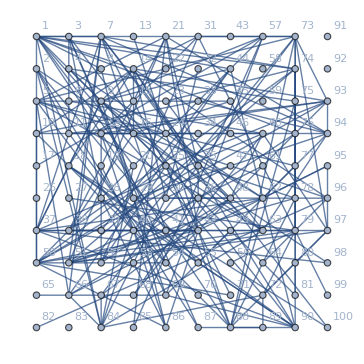

```mathematica
For[j=1, j<4,j++, 
For[i=1, i≤ Length[indices],i++,
index = Part[RandomChoice[DeleteCases[Range[1,100],Part[indices,i]],1],1];
Part[mat, Part[indices,i],  index] = 1;
Part[mat, index,  Part[indices,i]] = 1;
];
];
indices = DeleteDuplicates[Flatten[SparseArray[mat]["AdjacencyLists"]]];m = mat // MatrixForm;
g1 = AdjacencyGraph[mat];count = count + 1; Print["Elapsed: ", count* 30, " minutes, People: ", Length[Part[ConnectedComponents[g1],1]]];
g2=Graph[VertexList[g],EdgeList[g1],VertexCoordinates->GraphEmbedding[g],VertexSize->Medium, VertexLabels->Automatic]
```

## Introduction to Random Graphs

In mathematics, random graph is the general term to refer to a probability space over graphs, thus a random graph is described by a probability distribution or by a random process, which generates it. From a mathematical perspective, random graphs are used to answer questions about the properties of typical graphs.  For  example,  it  offers a way to study  how  the  connectivity  of a random graph evolves as the number of edges increases.

### Brief History of Random Graphs

Key ideas already appeared in sociology and biophysics [7; 8]

Mathematical foundation by Paul Erdős and  Alfréd  Rényi  "On  random  Graphs",  published  in  1959 [3] and then a seminal series of papers

Different approach by Edgar Gilbert in  “Random graphs” [5]

Duncan J. Watts and Steven Strogatz bringing random graphs closer to real-world networks [9]

Systematical study of random networks and general network science by Albert Barabási [1; 2]

-Graphics-

Random Graphs : The Intersection of Different Fields

## Introduction to Random Graphs

Consider the sample space 𝒮 consisting of graphs with 3 vertices {𝓋, 𝓊, 𝓌} and 2 edges in between. If we define a probability function 𝒫, which assigns each graph in this sample space with equal probability, then (𝒮, 𝒫) defines a discrete probability space which is know as an Erdős-Rényi Random Graph.

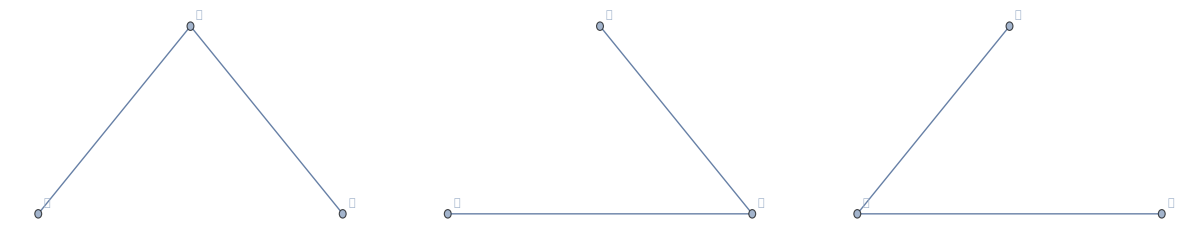

```mathematica
GraphicsGrid[{{Graph[{𝓋<->𝓌,𝓌<->𝓊},VertexCoordinates->{𝓋->{0,0},𝓌->{1,1}, 𝓊->{2, 0}},VertexLabels->"Name"], Graph[{𝓋<->𝓊,𝓌<->𝓊},VertexCoordinates->{𝓋->{0,0},𝓌->{1,1}, 𝓊->{2, 0}},VertexLabels->"Name"], Graph[{𝓋<->𝓌,𝓋<->𝓊},VertexCoordinates->{𝓋->{0,0},𝓌->{1,1}, 𝓊->{2, 0}},VertexLabels->"Name"]}}]
```

Random graph on {𝓋, 𝓊, 𝓌} with 2 edges

### Definition: Erdős-Rényi Random Graph

Let 𝒱 be a set of 𝓃 vertices, and let 𝓂 ∈ ℕ denote the number of edges. Then an Erdős Rényi Random Graph, also called Uniform Random Graph 𝒢(𝓃, 𝓂) is the uniform probability space on the set of all graphs with vertices 𝒱 and 𝓂 edges.

In particular |𝒱| = 𝓃 implies that there can be at most  (n
2) edges. Therefore there are ((n
2) 
𝓂) graphs with 𝓂 edges and 𝓃 vertices, and the probability function assigns each of them with equal probability. It follows that the probability of a particular graph is 𝒫(𝒢(𝓃, 𝓂) = G) = ((n
2) 
𝓂)^-1 .

## Binomial Random Graphs

### Definition: Gilbert Random Graph

Let 𝒱 be a set of 𝓃 vertices, and let 0 ≤ 𝓅 ≤ 1 be the common probability of joining any two of these vertices. Then a Gilbert Random Graph or Binomial Random Graph, denoted 𝒢(𝓃, 𝓅) is the binomial probability space on the set of all graphs with vertices 𝒱.

This definition only fixes the number of nodes, and not the number of edges. In particular each edge of (n
2)  can be present or not, which yields the size of the sample space that is 2^(n
2). Moreover the probability of sampling any one of these graphs G is 𝒫(𝒢(𝓃, 𝓅) = G) =𝓅^𝓂(1-𝓅)^((n
2)-𝓂).

## Binomial Random Graphs

### Proposition: Edge Distribution

Let 𝒳 be a random variable denoting the number of edges in a binomial random graph, with 𝓃 nodes and parameter 𝓅. Then 𝒫(𝒳 = 𝓂) =( (n
2)
𝓂) 𝓅^𝓂 (1-𝓅)^((n
2)-𝓂),  and 𝔼(𝒳) = 𝓅(n
2).

#### Proof:

Let 𝒳 be a random variable denoting the number of edges in G. Then there are (n
2) choose 𝓂 ways of picking a graph with 𝓂 edges and a 𝓃 vertices, each of which has probability as in the previous slide. As these are all mutually independent events, the overall probability is as above. This means that 𝒳 has the binomial distribution as well, in which case its expectation value is 𝓅 (n
2).

### Proposition: Degree Distribution

Let 𝒳 be a random variable denoting the degree of an arbitrary vertex 𝓋 in a binomial random graph, with 𝓃 nodes and parameter 𝓅. Then 𝒫(𝒳 = k) =(𝓃-1
𝓀) 𝓅^𝓀 (1-𝓅)^((𝓃-1)-𝓀),  and 𝔼(𝒳) = 𝓅(𝓃-1).

#### Proof

Consider a vertex 𝓋 in a Gilbert random graph 𝒢(𝓃, 𝓅), and let 𝒳 = deg(𝓋) be as above, and 𝓀 ∈ ℕ. Then to have deg(𝓋) = 𝓀, we require 𝓀 nodes out of the remaining 𝓃-1, as self loops are excluded, each of these subgraphs has probability  𝓅^𝓀 (1-𝓅)^((𝓃-1)-𝓀), and so the overall probability can be derived from the disjoint union of these events. It follows again from the binomial distribution that the expectation value is 𝓅(𝓃-1).

## Binomial Random Graphs

### Definition: Hub

Let G = (V, E) be a graph. Then a hub H is a subset of V with the property that for any pair of vertices in H \ V, there is a path between them with intermediate vertices all in H.
Informally Speaking Hubs are vertices with large degrees, often significantly larger than the average degree ⟨𝓀⟩. It is easy to see using Stirling’s approximation and the Poisson distribution that the probability of hubs decreases rapidly. This can also bee seen on the distributions themselves.

### Approximating the Degree Distribution

Probability Theory tells us that whenever we have a binomial distribution, we may approximate it with the Poisson distribution for 𝓀≪ 𝓃, i.e. when the number of nodes is far greater than the average degree of a vertex. In this case we get that 𝒫(deg(𝓋) = k) ≃ e^(-𝓅(𝓃 - 1))  ((𝓅^𝓀(𝓃-1))^𝓀)/(𝓀!):= e^(-⟨𝓀⟩) ⟨𝓀⟩^𝓀/(𝓀!).

```mathematica
Manipulate[Show[DiscretePlot[Table[PDF[BinomialDistribution[100, p], k], {p, {x/100}}] // Evaluate, {k, 100}, PlotRange -> All, PlotMarkers -> Automatic, PlotLegends->LineLegend[{"Binomial"}]], DiscretePlot[Table[PDF[PoissonDistribution[λ],k],{λ,{x}}]//Evaluate,{k,100},PlotRange->All,PlotMarkers->Automatic, PlotStyle->Red, PlotLegends->LineLegend[{"Poisson"}]]],{x, 20, 100}]
```

## Binomial Random Graphs

A more local property of random graphs than hubs are so called, clusters.  The idea comes from social networks. For example, consider a group of friends. Then we expect them to all know each other, whereas in a group of acquaintances some introductions are yet to be made.  In order to capture this phenomenon first we need the following definitions.

### Definition: Clustering Coefficient

Let G = (V, E) be a graph, and let λ(𝓋) denote the number of triangles on 𝓋 (3 edges, 3 vertices one of which is 𝓋). Similarly let τ(𝓋) denote the number of triples on 𝓋 (2 edges, 3 vertices one of which is 𝓋). Then the Local Clustering Coefficient of 𝓋 is defined as 𝒞_𝓋= (λ(𝓋))/(τ(𝓋)). The Average Clustering Coefficient of a graph G is defined as the mean of all the 𝒞_𝓌 where 𝓌 ∈ V, and can be denoted by OverBar[𝒞_G].

### Proposition: Expected Clustering Coefficient

Let 𝒢(𝓃, 𝓅) be a binomial random graph and 𝓋 one of its vertices, then 𝔼(𝒞_𝓋) = 𝓅.

#### Proof:

We have seen that the expected number of edges in 𝒢(𝓃, 𝓅) is 𝓅 (n
2). Therefore among 𝓀 edges, we expect to have 𝓅 (𝓀
2) = 𝓅(𝓀(𝓀-1))/2 edges. Therefore 𝔼(𝒞_𝓋) = 𝔼((λ(𝓋))/(τ(𝓋))) = (𝔼(λ(𝓋)))/((𝓀(𝓀-1))/2)=(𝓅(𝓀(𝓀-1))/2)/((𝓀(𝓀-1))/2)= 𝓅, as λ(𝓋) can also be counted as the number of edges between vertices adjacent to 𝓋, with deg(𝓋) = 𝓀. As this holds for any vertex 𝓋, the average clustering coefficient of a binomial random graph is also 𝓅.

## Binomial Random Graphs

### Connectivity

We have seen how the number of edges or the degree of vertices are likely to behave in random graphs, but we have not seen whether this graph should be connected or a collection of isolated edges? Inspired by telephone networks, this was the problem Gilbert investigated in 1959 [5].

```mathematica
Manipulate[Plot[Count[ConnectedGraphQ/@RandomGraph[BernoulliGraphDistribution[n,p],100], True], {p,0,1}, AxesLabel->{p, "% of Connected Graphs"}],{n,1, 100,1}]
```

We can see that for every 𝓃, there is a 0 ⩽ 𝓅 ⩽ 1 such that most graphs are connected. More interestingly for most 𝓃, 𝓅 ≪ 1 suffices, this is because as 𝓃 grows, we have more and more Bernoulli trials. This little experiment is in line with Gilbert’s more rigorous results, showing that the probability of a connected graph as 𝓃 grows goes to 1.

## Average Path Lengths

Having shown that a binomial random graph is almost certain to be connected as 𝓃 grows large.  It makes sense to ask, about the distance between two nodes as 𝓃 → ∞. We will first define this distance rigorously, and then provide a rough estimate with the help of the diameter.

### Definition: Distance & Average Path Length

Let G = (V, E) be a graph and 𝓊, 𝓋 ∈ V. Then d(𝓊, 𝓋) is called the distance between 𝓊 and 𝓋, and is defined to be the number of nodes on the shortest path between them. If 𝓊 and 𝓋 are not connected, we defined d(𝓊, 𝓋) = 0. The Average (Shortest) Path Length of a graph G=(V, E) is then defined as ℓ_G= ∑_(𝓊,𝓋 ∈ V, 𝓊≠𝓋) (d(𝓊,𝓋))/(𝓃(𝓃 - 1)), sometimes called the APL.

### Definition: Diameter

Let G = (V, E) be a graph, then the maximal distance between all the pairs of nodes of G is called the diameter of G. More formally: 𝒹_max =  max{d(𝓊, 𝓋) | 𝓊, 𝓋 ∈ V}.

### Proposition: Approximation for the Diameter [2]

In a binomial random graph with 𝓃 vertices and average degree ⟨𝓀⟩, we have 𝒹_max ≈ (ln(n))/(ln⟨𝓀⟩).

#### Proof:

Consider a binomial random graph with 𝓃 vertices and average degree ⟨𝓀⟩. Then a node 𝓋 has on average ⟨𝓀⟩ vertices at distance 1. Since each of these vertices has average degree ⟨𝓀⟩, the expected number of vertices at distance 2 is ⟨𝓀⟩^2. Continuing with this method 𝓋 has on average ⟨𝓀⟩^𝒹_max vertices at distance 𝒹_max, and no nodes any further than that. As we have seen most random graphs are connected, and so the sum 1 + ⟨𝓀⟩ + ... + ⟨𝓀⟩^𝒹_max = (⟨𝓀⟩^(𝒹_(max + 1))-1)/(⟨𝓀⟩ - 1)≈ ⟨𝓀⟩^(𝒹_(max + 1))/⟨𝓀⟩= ⟨𝓀⟩^𝒹_max should not exceed the overall number of nodes 𝓃. Taking the natural logarithm and rearranging we get 𝒹_max ≈ (ln(n))/(ln⟨𝓀⟩).

## Average Path Lengths

In fact  Fronczak, Fronczak and Holyst [4] were able to find analytic formula for the average path length for many random graphs, including the Gilbert random graph in the  models limiting case 𝓃 → ∞. To achieve this we let 𝓅 to vary with 𝓃. More specifically, for fixed average degree ⟨𝓀⟩, they defined 𝓅(𝓃) = ⟨𝓀⟩/(n-1). This is similar to Fronczak et al. , as they defined 𝓅 as a function of hidden variables depending on the nodes it connects.

### Lemma: Probability of Mutually Independent Events

If 𝒜_1, 𝒜_2,..., 𝒜_𝓃 are mutually independent events and their probabilities fulfill 𝒫(𝒜_𝒾) ≤ ℰ for every 𝒾, then for 0 ≤ 𝒬 ≤ ∑_(𝒿=0)^(𝓃+1) (𝓃ℰ)^𝒿/ 𝒿! - (1+ℰ)^𝓃 we have that:

𝒫(∪_(𝒾 = 1)^𝓃𝒜_𝒾) = 1 - exp(- ∑ _(𝒾=1)^𝓃 𝒫(𝒜_𝒾)) - 𝒬

#### Proof

See Project Report.

### Formula: APL

Using the Lemma above, the Poisson Summation Formula and the Generalized Mean Value Theorem Fronzcak et al. was able to derive an exact formula for the average path length of a binomial random graph. The formula states that for γ ≈ 0.5772 (Euler’s constant) the APL is:

ℓ_G = 1/2 + (ln(𝓃) - γ)/(ln⟨𝓀⟩)

## Average Path Lengths

Deriving the formula would be too long to be contained in this presentation. There are, however, significant assumptions Fronczak et al. make in order to arrive at the result. Although by consulting with the authors most steps became clear, some will have to be considered with criticism.

### Assumptions and Criticism:

The proof starts by considering a walk of length 𝓀 in 𝒢(𝓃, 𝓅). Now by the definition of a walk, the vertices do not have to be distinct, only adjacent. In case an edge appears in this walk twice however, it is guaranteed to be present in the graph for the second time, and hence it exists with probability 𝓅 and not 𝓅^2. Fronczak et al. assumes that the probability of the existence of such a walk is 𝓅^𝓀, whereas really we only know is that it lies in [𝓅^𝓀, 𝓅^1].

Now fix vertices 𝓊 and 𝓋, and let 𝒜_(𝓌_1, ..., 𝓌_(𝓀-1))denote the event that there is a walk of length 𝓀 between them through vertices 𝓌_1, ..., 𝓌_(𝓀-1). Fronczak et al. requires these events to be mutually independent to apply the lemma from before, but we may see that as an edge may appear in more than one walk, these events are not mutually independent.

Not specifying the theorem used in showing the convergence of the series in the Poisson Summation Formula.

## Average Path Lengths

### Experimental Outcomes

```mathematica
Manipulate[Show[DiscretePlot[MeanGraphDistance[RandomGraph[BernoulliGraphDistribution[n,k/(n-1)]]],{n, 10, 100}, PlotMarkers->Automatic,AxesLabel->{"n", "APL"}, PlotLegends->LineLegend[{"Data Points"}]],Plot[ 0.5+((Log[n]-EulerGamma) / (Log[k])),{n, 10, 100}, PlotStyle->Red, PlotLegends->LineLegend[{"Formula"}]]],{n,10,1000, 10}, {k, 5, 100, 5}]
```

Experiments show that the formula converges to the expected APL, but as the average degree increases, the larger we require 𝓃 to be to get a good approximation.

## The Small-World Property

The small-world phenomenon, also known as six degrees of separation, has long fascinated the general public for its surprising statement that if you choose two individuals anywhere on Earth, you will find a path of at most six acquaintances between them [6].  But how does this translate to the study of random graphs?

Although small-world networks do not have a word-by-word definition, more specifically, a small-world network is a graph, whose average path length grows proportional to the logarithm of the number of nodes, while the average clustering coefficient is not low. To summarise Small-World network G, with 𝓃 nodes, we have:

𝒪(ℓ_G(𝓃)) = 𝒪(ln(𝓃)). 						✓

0 ≪ OverBar[𝒞_G]. 							𝒳

Presence of highly connected sub-networks, called cliques.	?

High number of hubs.						𝒳

Smoother degree distribution (tail).				𝒳

### Real-World Networks

Many real-world networks posses the small-world property, which our random graph model fails to create. Comparing the relevant metrics of some real-world networks we see that the APL is similar, but the clustering in random networks is higher.

Real-world networks

## The Small-World Property

Although the simplicity of Gilbert random graphs has made the model an attractive choice for many applications, their degree distributions and clustering coefficients do not resemble networks observed in the real world. To address these differences an alternative model was proposed in [9], called the Watts-Strogatz model.

### Definition: Watts-Strogatz Random Graph

Let 𝓃 denote the number of vertices and let 𝓀 be an even integer, denoting the average degree of a vertex. Furthermore, assume that 𝓃 ≫ 𝓀 ≫ ln(𝓃) ≫ 1, and let 0 ≤ 𝓅 ≤ 1. Then constructing a Watts-Strogatz Random Graph consists of two steps (more formally see the Project Report):

Arrange the 𝓃 vertices in a ring lattice, then connect each vertex with 𝓀/2 of its neighbours (on the lattice) on either side.

For each vertex rewire every edge by choosing uniformly between the remaining vertices, while disallowing multiple edges.

```mathematica
Manipulate[Graph[RandomGraph[WattsStrogatzGraphDistribution[n,p,k]], GraphLayout->{"CircularEmbedding","OptimalOrder"->False}],{n,10,100,10},{p, 0,1}, {k,1, n/2,1}]
```

## The Small-World Property

The condition 𝓃 ≫ 𝓀 will yield large sparse graphs, while 𝓀 ≫ ln(𝓃) ≫ 1 guarantees that the graph does not become disconnected. Moreover as 𝓅 → 0 we have seen that the Watts-Strogatz Model generates a regular ring lattice, in which case the Average Clustering Coefficient is given by (3(𝓀-2))/(4(𝓀-1))≈3/4, and the Average Path Length is approximately 𝓃/(2𝓀), where 𝓀 is the average degree of a vertex, and 𝓃 is the number of nodes [9].

As 𝓅 → 1, however, the model starts to resemble a binomial random graph with 𝓅 = 𝓀/(𝓃-1), while not exactly converging to it, as the minimum number of edges in the Watts-Stogatz model is set to 𝓃𝓀/2. Therefore at the other end of the spectrum the APL is approximately (ln(𝓃))/(ln(𝓀)), and the Average Clustering is approximately 𝓀/𝓃 [9]. This leaves an interval of possibility for Small-World networks to emerge between the two extremes.

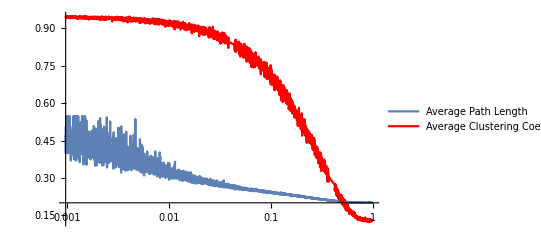

```mathematica
Show[LogLinearPlot[MeanGraphDistance[RandomGraph[WattsStrogatzGraphDistribution[200,p,10]]]/ (200/(2*10)),{p, 0,1},PlotLegends->LineLegend[{"Average Path Length"}], PlotRange->All],LogLinearPlot[MeanClusteringCoefficient[RandomGraph[WattsStrogatzGraphDistribution[200,p, 10]]]/ (0.75),{p, 0,1},PlotStyle->Red, PlotLegends->LineLegend[{"Average Clustering Coefficient"}], PlotRange->All]]
```

## The Small-World Property

Let’s see what kind of graphs we get with this model. Given 400 people, all having 4 acquaintances, what is the average number of introductions needed to reach anyone in the network?

```mathematica
<<"IGraphM`"
```

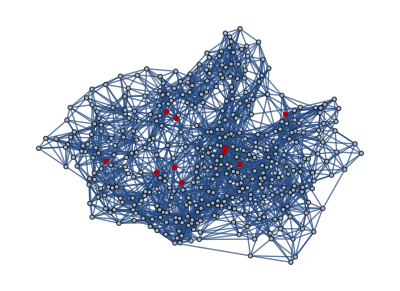

Before Rewiring: 0.479883 6.91729

After Rewiring: 0.397906 3.63623

```mathematica
g1=IGMakeLattice[{20,20},Radius->2];
g2 = Graph[IGRewireEdges[g1,0.03]];
HighlightGraph[g2, GraphHub[g2]]
Print["Before Rewiring: ", N@MeanClusteringCoefficient[g1]," ",IGAveragePathLength[g1]]
Print["After Rewiring: ", N@MeanClusteringCoefficient[g2]," ",IGAveragePathLength[g2]]
```

## Conclusion

We  will  close  by  asking  the  same  question  as Barabási in [2],  namely: Are  real  world  networks  truly  random? The answer, as Barabási put it, “is clearly no”.  In reality, it is more likely that complex systems appear as a result of some deep underlying order behind all the chaos.  However, by studying random graphs, we were able to quantify some of these differences, and even explore ideas that tried to patch the discrepancies.

In fact the theory of random graphs serves more as a reference point when studying real-world networks.  Upon discovering a new property of a network, a question random graphs can answer is: if it could have emerged by chance? If the property cannot be found in random graphs, it may represent a signature of order, “requiring a deeper explanation” [2].  This is the relevance of random graphs to the study of networks.

## References

[1]  Réka Albert and Albert-László Barabási.  Statistical mechanics of complex networks. Reviews of modern physics, 74(1):47, 2002.

[2]  Albert-László Barabási.  Linked:  The new science of networks, 2003.

[3]  Paul Erdős and Alfréd Rényi.  On the evolution of random graphs. Publ.Math. Inst. Hung. Acad. Sci, 5(1):17–60, 1960.

[4]  Agata Fronczak, Piotr Fronczak, and Janusz A Holyst. Average path length in random networks. Physical Review E, 70(5):056110, 2004.

[5]  Edgar N Gilbert.  Random graphs. The Annals of Mathematical Statistics, 30(4):1141–1144, 1959.

[6]  Stanley  Milgram.   Six  degrees  of  separation.Psychology Today,  2:60–64,1967.

[7]  Jacob L Moreno and Helen H Jennings.  Statistics of social configurations. Sociometry, pages 342–374, 1938.

[8]  Ray Solomonoff and Anatol Rapoport.  Connectivity of random nets.The bulletin of mathematical biophysics, 13(2):107–117, 1951.

[9]  Duncan  J  Watts  and  Steven  H  Strogatz.   Collective  dynamics  of  'small-world' networks. nature, 393(6684):440–442, 1998.

## Any Questions?